```mathematica
Text[Grid[Table[LCM[i,j]^2,{i,20},{j,12}],Frame->All,Alignment->Right,Background->{None,{{LightPink,LightBlue,LightGreen}}}]]
```

1 | 4 | 9 | 16 | 25 | 36 | 49 | 64 | 81 | 100 | 121 | 144
4 | 4 | 36 | 16 | 100 | 36 | 196 | 64 | 324 | 100 | 484 | 144
9 | 36 | 9 | 144 | 225 | 36 | 441 | 576 | 81 | 900 | 1089 | 144
16 | 16 | 144 | 16 | 400 | 144 | 784 | 64 | 1296 | 400 | 1936 | 144
25 | 100 | 225 | 400 | 25 | 900 | 1225 | 1600 | 2025 | 100 | 3025 | 3600
36 | 36 | 36 | 144 | 900 | 36 | 1764 | 576 | 324 | 900 | 4356 | 144
49 | 196 | 441 | 784 | 1225 | 1764 | 49 | 3136 | 3969 | 4900 | 5929 | 7056
64 | 64 | 576 | 64 | 1600 | 576 | 3136 | 64 | 5184 | 1600 | 7744 | 576
81 | 324 | 81 | 1296 | 2025 | 324 | 3969 | 5184 | 81 | 8100 | 9801 | 1296
100 | 100 | 900 | 400 | 100 | 900 | 4900 | 1600 | 8100 | 100 | 12100 | 3600
121 | 484 | 1089 | 1936 | 3025 | 4356 | 5929 | 7744 | 9801 | 12100 | 121 | 17424
144 | 144 | 144 | 144 | 3600 | 144 | 7056 | 576 | 1296 | 3600 | 17424 | 144
169 | 676 | 1521 | 2704 | 4225 | 6084 | 8281 | 10816 | 13689 | 16900 | 20449 | 24336
196 | 196 | 1764 | 784 | 4900 | 1764 | 196 | 3136 | 15876 | 4900 | 23716 | 7056
225 | 900 | 225 | 3600 | 225 | 900 | 11025 | 14400 | 2025 | 900 | 27225 | 3600
256 | 256 | 2304 | 256 | 6400 | 2304 | 12544 | 256 | 20736 | 6400 | 30976 | 2304
289 | 1156 | 2601 | 4624 | 7225 | 10404 | 14161 | 18496 | 23409 | 28900 | 34969 | 41616
324 | 324 | 324 | 1296 | 8100 | 324 | 15876 | 5184 | 324 | 8100 | 39204 | 1296
361 | 1444 | 3249 | 5776 | 9025 | 12996 | 17689 | 23104 | 29241 | 36100 | 43681 | 51984
400 | 400 | 3600 | 400 | 400 | 3600 | 19600 | 1600 | 32400 | 400 | 48400 | 3600

```mathematica
GraphicsGrid[Table[KnotData[{i,j}],{i,6,8},{j,3}],Frame->All]
```

-Graphics-

```mathematica
Grid[Table[RandomChoice[{Slider[ImageSize->Tiny],Checkbox[]}],{15},{5}],Frame->All]
```

|  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  | 
 |  |  |  |

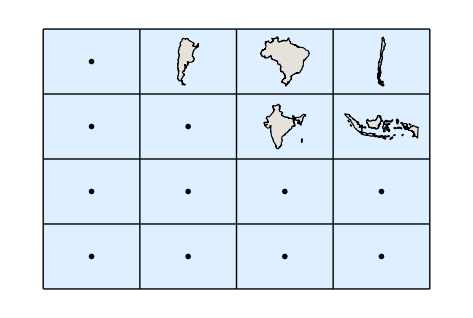

```mathematica
GraphicsGrid[Partition[CountryData[#,"Shape"]&/@CountryData["GroupOf15"],4],Background->LightBlue,Frame->All]
```

```mathematica
GraphicsGrid[Partition[GraphData/@GraphData[12],8],Background->{{{LightYellow,LightBlue}}}]
```

-Graphics-

```mathematica
Grid[Table[RandomChoice[{SpanFromLeft,SpanFromAbove,Item[RandomInteger[1000],Background->Hue[RandomReal[],.2,.9]]}],{30},{15}],Frame->All]
```

|  | 617 | 213 |  |  |  |  | 946 | 656 |  |  | 673 | 799 | 
 | 869 | 626 | 686 |  | 132 | 662 | 963 |  |  |  | 248 | 275 |  | 
 | 150 |  |  |  |  |  |  |  |  | 461 |  |  | 700 | 410
 |  | 798 |  | 344 | 477 | 968 |  | 438 |  |  |  |  |  | 498
564 | 638 |  |  |  |  |  | 562 |  |  | 317 | 652 |  |  | 
835 |  | 70 |  | 307 |  |  |  |  |  |  |  |  |  | 
 | 472 | 157 |  | 448 |  | 865 |  |  |  |  |  |  |  | 
 |  | 327 |  | 7 |  |  |  |  |  |  |  | 855 | 587 | 508
 |  | 516 |  |  |  |  | 522 |  |  |  | 412 |  |  | 
 | 257 |  |  | 939 | 367 |  | 735 | 763 |  |  |  |  |  | 204
 |  |  |  |  |  | 208 |  |  |  |  |  |  |  | 
517 |  | 959 |  |  |  | 28 |  | 857 |  | 881 |  |  |  | 
 |  |  | 556 |  |  |  |  |  | 218 | 481 | 276 | 533 | 476 | 784
180 |  |  |  |  |  |  | 36 |  |  |  |  | 234 |  | 378
 |  |  | 681 |  |  |  |  |  | 544 |  |  |  |  | 
849 | 630 |  | 814 |  |  |  |  | 33 |  | 120 | 908 |  | 516 | 
609 |  |  | 341 | 440 |  | 875 |  | 146 |  |  | 232 | 229 | 471 | 304
290 |  |  |  | 801 |  |  | 285 |  | 549 |  |  |  |  | 264
 | 480 | 707 | 529 |  | 894 |  | 609 |  | 915 |  |  | 476 |  | 
 | 569 |  | 170 |  | 652 | 942 | 987 |  | 500 | 528 |  | 170 |  | 
 | 686 |  | 45 | 213 | 390 |  |  | 918 | 280 |  |  |  | 328 | 
 |  | 198 |  |  |  |  | 111 | 830 |  |  |  | 373 |  | 
 |  |  | 983 |  | 499 |  |  | 174 | 380 |  |  |  | 219 | 
 |  |  |  |  |  | 729 |  | 325 | 810 | 798 | 895 | 351 | 890 | 
546 |  | 228 |  | 39 |  |  | 712 |  |  |  | 148 |  | 216 | 
451 |  |  | 508 | 368 |  | 605 |  | 251 | 118 |  |  |  | 443 | 188
470 | 920 | 823 |  |  | 837 |  |  |  | 777 |  |  | 935 |  | 
 |  | 362 |  |  | 47 |  |  | 132 |  | 311 | 912 |  | 884 | 
514 |  | 185 | 694 | 188 |  | 157 |  | 820 |  | 232 |  |  |  | 
 |  |  |  |  | 125 |  |  |  |  |  |  | 651 | 795 | 639

```mathematica
Text[Grid[Table[With[{n=n},With[{u=HoldForm[∫1/(x^n-1) ⅆx]},TraditionalForm/@{u,ReleaseHold[u]}]],{n,8}],Frame->All,ItemSize->Automatic,Background->LightYellow]]
```

∫1/(x^1-1)ⅆx | log(x-1)
∫1/(x^2-1)ⅆx | 1/2 log(1-x)-1/2 log(x+1)
∫1/(x^3-1)ⅆx | -1/6 log(x^2+x+1)+1/3 log(1-x)-(tan^-1((2 x+1)/(√3)))/(√3)
∫1/(x^4-1)ⅆx | 1/4 log(1-x)-1/4 log(x+1)-1/2 tan^-1(x)
∫1/(x^5-1)ⅆx | 1/20 ((√5-1) log(x^2-1/2 (√5-1) x+1)-(1+√5) log(x^2+1/2 (1+√5) x+1)+4 log(1-x)-2 √(2 (5+√5)) tan^-1((4 x-√5+1)/(√(2 (5+√5))))-2 √(10-2 √5) tan^-1((4 x+√5+1)/(√(10-2 √5))))
∫1/(x^6-1)ⅆx | 1/12 (log(x^2-x+1)-log(x^2+x+1)+2 log(1-x)-2 log(x+1)-2 √3 tan^-1((2 x-1)/(√3))-2 √3 tan^-1((2 x+1)/(√3)))
∫1/(x^7-1)ⅆx | 1/7 sin((3 π)/14) log(x^2-2 x sin((3 π)/14)+1)-1/7 sin(π/14) log(x^2+2 x sin(π/14)+1)-1/7 cos(π/7) log(x^2+2 x cos(π/7)+1)+1/7 log(1-x)-2/7 sin(π/7) tan^-1(csc(π/7) (x+cos(π/7)))-2/7 cos((3 π)/14) tan^-1(sec((3 π)/14) (x-sin((3 π)/14)))-2/7 cos(π/14) tan^-1(sec(π/14) (x+sin(π/14)))
∫1/(x^8-1)ⅆx | 1/16 (√2 log(x^2-√2 x+1)-√2 log(x^2+√2 x+1)+2 log(1-x)-2 log(x+1)-4 tan^-1(x)+2 √2 tan^-1(1-√2 x)-2 √2 tan^-1(√2 x+1))

```mathematica
NestList[Grid[{{#,#},{#,#}},Frame->All]&,x,4]
```

{x,x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x,x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x | x | x
x | x | x | x
x | x
x | x
x | x | x | x
x | x}

```mathematica
Grid[Table[ChemicalData["Caffeine","MoleculePlot"],{2},{2}],Frame->All]
```

-Graphics3D- | -Graphics3D-
-Graphics3D- | -Graphics3D-

```mathematica
Plot3D[Evaluate[Table[Tooltip[Sin[x+n y],Plot[Sin[n x],{x,0,2 Pi},Filling->Axis,FillingStyle->Pink,ImageSize->200]],{n,3}]],{x,0,3},{y,0,3},PlotStyle->Table[Opacity[.7,Hue[i/6]],{i,4}]]
```

-Graphics3D-

```mathematica
Graphics3D[Table[{Hue[RandomReal[]],Opacity[RandomReal[]],Specularity[White,20],Sphere[RandomReal[6,3]]},{50}]]
```

-Graphics3D-

```mathematica
GraphicsGrid[Table[Graphics3D[{Yellow,Opacity[.5],PolyhedronData["SnubCube","Faces"]},ViewVector->RandomReal[2,3],ViewAngle->RandomReal[{.3,3}],Boxed->False],{4},{4}],Frame->All]
```

-Graphics-

```mathematica
GraphicsGrid[Table[Graphics3D[{Specularity[White,30],Sphere[]},Lighting->Table[{"Spot",ColorData["Rainbow",RandomReal[]],RandomReal[{-5,5},3],30 °},{4}]],{3},{3}]]
```

-Graphics-

```mathematica
p1[θ_]:=RotationTransform[θ,{0,0,1}][{0,2,0}];
```

```mathematica
p2[θ_]:=RotationTransform[θ+Pi/2,{1,0,1}][{0,2,0}];
```

```mathematica
p3[θ_]:=RotationTransform[θ+Pi,{1,0,0}][{0,2,0}];
```

```mathematica
p4[θ_]:=RotationTransform[θ+3 Pi/2,{1,0,-1}][{0,2,0}];
```

```mathematica
Animate[Graphics3D[{Specularity[White,30],Sphere[],Sphere[p1[θ],.4],Sphere[p2[θ],.4],Sphere[p3[θ],.4],Sphere[p4[θ],.4]},Lighting->{{"Ambient",GrayLevel[.1]},{"Point",Red,p1[θ]},{"Point",Green,p2[θ]},{"Point",Blue,p3[θ]},{"Point",Yellow,p4[θ]}},PlotRange->2.5,Boxed->False],{θ,0,2 Pi},SaveDefinitions->True]
```